```mathematica
SetOptions[EvaluationNotebook[],AutoGeneratedPackage->Automatic]
```

# Complex Variables Toolkit - Final Project

## This package will contain many visualization tools that allows one to understand how complex functions behave

## Complex plane to image plane

### makeImage takes in a list of points, a complex function, and two plot ranges and outputs the original and its image.

```mathematica
makeImage[pts_,expr_,pltRange1_:Automatic,PltRange2_:Automatic,colors_:1]:=Module[{},
If[colors==1,colors=RGBColor[1,1,1],colors=colors];
{
Graphics[MapThread[{#1, Thick, Line[#2]}&,{colors,pts}], PlotRange -> pltRange1, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["x",Italic], Style["y",Italic]},ImagePadding->20],

Graphics[MapThread[{#1, Thick, Line[{Re[expr /. z -> #[[1]] + ⅈ #[[2]]], Im[expr /. z -> #[[1]] + ⅈ #[[2]]]}& /@ #2]}&,{colors,pts}], PlotRange -> PltRange2, Axes -> True, Background -> White, ImageSize -> {300,300}, AxesLabel -> {Style["u",Italic], Style["v",Italic]},ImagePadding->20]
}
]
```

```mathematica
Dimensions@gridPts
```

{}

### makeCirclePoints will make expanding circles given smallest radius, largest radius, and a step size

```mathematica
makeCirclePoints[smallRadius_,largeRadius_,stepSize_]:=Module[
{ang, lists, pts},
ang=Range[0 Pi,2 Pi,.001];
lists=Table[{r Cos[ang],r Sin[ang]},{r,Range[smallRadius,largeRadius,stepSize]}];
pts=Transpose[#]&/@lists;
Return[pts]
]
```

{RGBColor[0.033932250154797394, 0.3982216960055087, 0.5811561215611634],RGBColor[0.1255473345530338, 0.896265281960787, 0.9924904791209304],RGBColor[0.7163631569989344, 0.6694626896938298, 0.5633544519376577],RGBColor[0.08121020469604989, 0.5806961032521791, 0.6979231392652461],RGBColor[0.002785398308525089, 0.09379197399914418, 0.05952676222967801],RGBColor[0.21129889401169333, 0.7176416526780607, 0.7485555352986286],RGBColor[0.7849604660586431, 0.8028358294388318, 0.9315848204720243]}

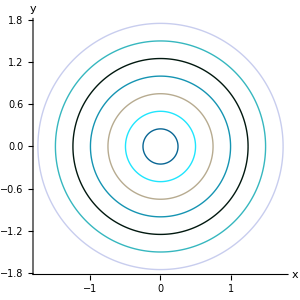
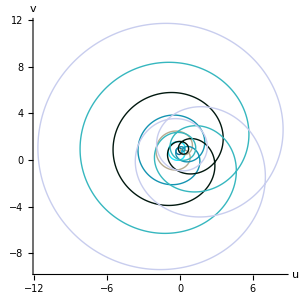

```mathematica
expr=(z+1)(z-.5)(z-1.5I);
pts=makeCirclePoints[.25,1.75,.25];
circleColors=makeRandomColors[pts]
n=2;
m=3;
makeImage[pts,expr,n,m,circleColors]
```

### makeGridPoints will make a grid of lines given user entered parameters

```mathematica
Clear[fSpace,makeVerticalPts,makeHorizontalPts,makeGridPts,makeLogVerticalPts,makeLogHorizontalPts,makeLogVerticalPts2,makeLogHorizontalPts2]
```

```mathematica
fSpace[min_,max_,steps_,f_: Log]:=Module[{},N[InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]]]
```

```mathematica
makeVerticalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{y,Range[min,max,(max-min)/(ptsPerLine-1)]}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]

makeHorizontalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,Range[min,max,(max-min)/(ptsPerLine-1)]}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]

makeGridPts[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeVerticalPts[min,max,ptsPerLine,numLines];
horiPts=makeHorizontalPts[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]

makeLogVerticalPts2[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts},
vertPts=Table[Table[{x,y},{y,fSpace[min,max,ptsPerLine]}],{x,min,max,(max-min)/(numLines-1)}];
Return[Re[vertPts]]
]

makeLogHorizontalPts2[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts},
horiPts=Table[Table[{x,y},{x,fSpace[min,max,ptsPerLine]}],{y,min,max,(max-min)/(numLines-1)}];
Return[Re[horiPts]]
]

makeLogGridPts[min_,max_,ptsPerLine_,numLines_]:=Module[{vertLogPts,horiLogPts,pts},
vertLogPts=makeLogVerticalPts[min,max,ptsPerLine,numLines];
horiLogPts=makeLogHorizontalPts[min,max,ptsPerLine,numLines];
pts=Join[horiLogPts,vertLogPts];
Return[pts]
]

makeLogVerticalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{posVertPts,negVertPts},
posVertPts=Table[Table[{x,y},{y,fSpace[.001,max,Floor[ptsPerLine/2]]}],{x,min,max,(max-min)/(numLines-1)}];
negVertPts=Table[Table[{x,y},{y,fSpace[min,-.001,Floor[ptsPerLine/2]]}],{x,min,max,(max-min)/(numLines-1)}];
pts=MapThread[Join,{negVertPts,posVertPts}];
Return[Re[pts]]
]

makeLogHorizontalPts[min_,max_,ptsPerLine_,numLines_]:=Module[{posHoriPts,negHoriPts},
posHoriPts=Table[Table[{x,y},{x,fSpace[.01,max,Floor[ptsPerLine/2]]}],{y,min,max,(max-min)/(numLines-1)}];
negHoriPts=Table[Table[{x,y},{x,fSpace[min,-.01,Floor[ptsPerLine/2]]}],{y,min,max,(max-min)/(numLines-1)}];
pts=MapThread[Join,{negHoriPts,posHoriPts}];
Return[Re[pts]]
]
```

### old

```mathematica
makeVerticalPts[start_,end_,stepSize_,lineSpacing_]:=Module[{vertPts},
newStep=stepSize+RandomReal[{.01,.02}];
vertPts=Table[Table[{x,y},{y,start,end,newStep}],{x,start,end,lineSpacing}];
Return[vertPts]
]

makeHorizontalPts[start_,end_,stepSize_,lineSpacing_]:=Module[{horiPts},
newStep=stepSize+RandomReal[{.01,.02}];
horiPts=Table[Table[{x,y},{x,start,end,newStep}],{y,start,end,lineSpacing}];
Return[horiPts]
]
```

```mathematica
makeRandomColors[pts_]:=Module[{colors},
colors=RandomColor[Length[pts]];
Return[colors]]
```

### Equal space test constants

```mathematica
numPts=1000;
numLines=3;
min=-10;
max=10;
expr=z^3
```

z^3

#### first make vertical lines

{7,1,2}

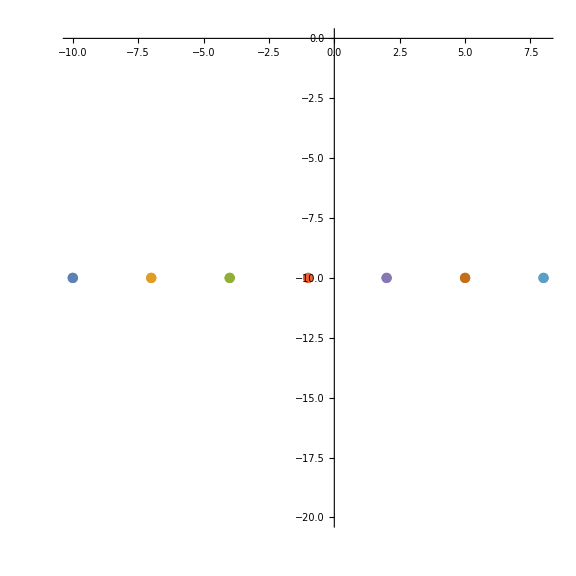

```mathematica
vertPts=makeVerticalPts[min,max,numPts,numLines];
Dimensions[vertPts]
ListPlot[vertPts,ImageSize->Large,AspectRatio->1]
```

#### second horizontal lines

{7,1,2}

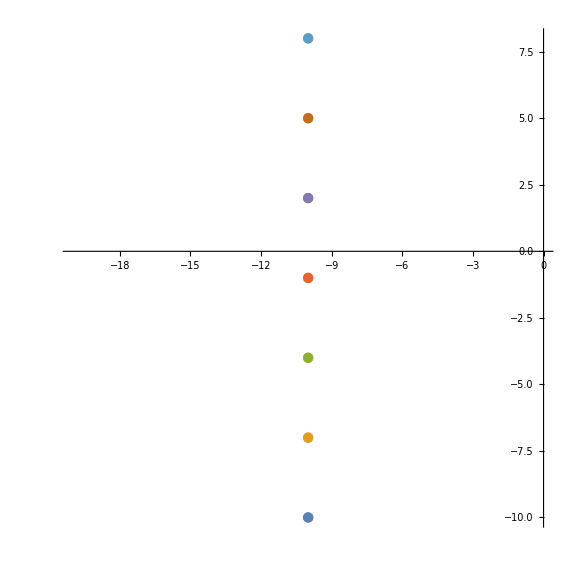

```mathematica
horiPts=makeHorizontalPts[min,max,numPts,numLines];
Dimensions[horiPts]
ListPlot[horiPts,ImageSize->Large,AspectRatio->1]
```

### Log test constants

```mathematica
ptsPerLine=100;
numLines=3;
min=-100;
max=100;
expr=z^3
```

z^3

{3,100,2}

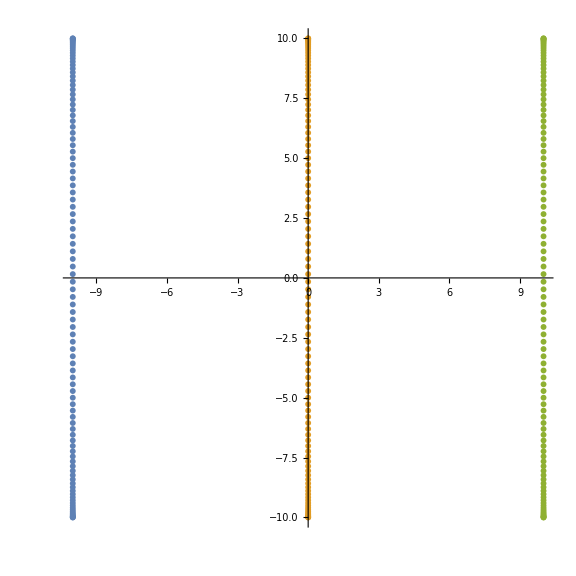

```mathematica
logVertPts=makeLogVerticalPts2[-10,10,ptsPerLine,numLines];
Dimensions[logVertPts]
ListPlot[logVertPts,ImageSize->Large,AspectRatio->1]
```

```mathematica
Range[-10,10,20/(21-1)]
```

{-10,-9,-8,-7,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Log[0]
```

-∞

```mathematica
N@Re@Log[Range[-3,3,1/10]]
```

{1.09861,1.06471,1.02962,0.993252,0.955511,0.916291,0.875469,0.832909,0.788457,0.741937,0.693147,0.641854,0.587787,0.530628,0.470004,0.405465,0.336472,0.262364,0.182322,0.0953102,0.,-0.105361,-0.223144,-0.356675,-0.510826,-0.693147,-0.916291,-1.20397,-1.60944,-2.30259,-∞,-2.30259,-1.60944,-1.20397,-0.916291,-0.693147,-0.510826,-0.356675,-0.223144,-0.105361,0.,0.0953102,0.182322,0.262364,0.336472,0.405465,0.470004,0.530628,0.587787,0.641854,0.693147,0.741937,0.788457,0.832909,0.875469,0.916291,0.955511,0.993252,1.02962,1.06471,1.09861}

#### first make vertical lines

{3,100,2}

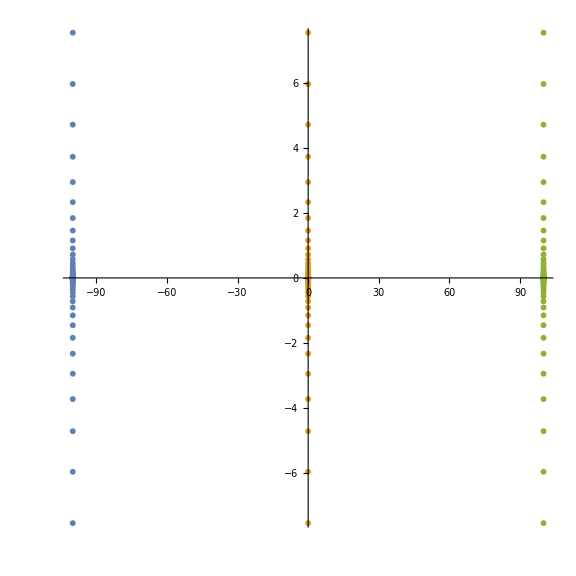

```mathematica
logVertPts=makeLogVerticalPts[min,max,ptsPerLine,numLines];
Dimensions[logVertPts]
ListPlot[logVertPts,ImageSize->Large,AspectRatio->1]
```

#### second horizontal lines

{3,100,2}

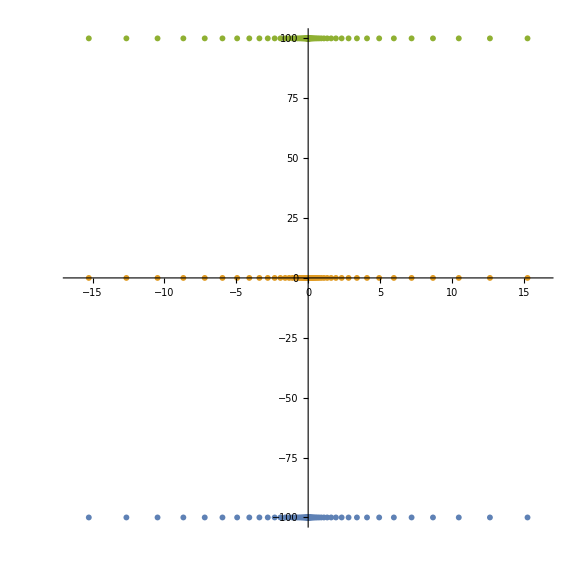

```mathematica
logHoriPts=makeLogHorizontalPts[min,max,ptsPerLine,numLines];
Dimensions[logHoriPts]
ListPlot[logHoriPts,ImageSize->Large,AspectRatio->1]
```

### Next try to make a grid

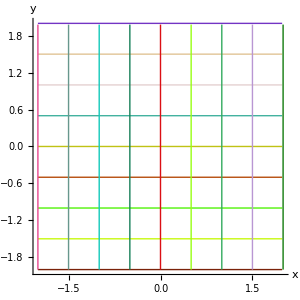
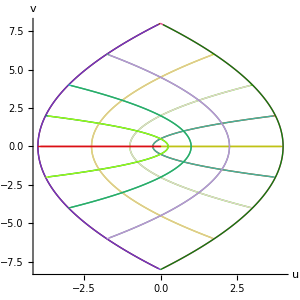

```mathematica
gridPts=makeGridPts[-2,2,.005,.5];
gridColors=makeRandomColors[gridPts];
makeImage[gridPts,z^2,Automatic,10,gridColors]
```

## Experiment with Riemann sphere stereographic projection

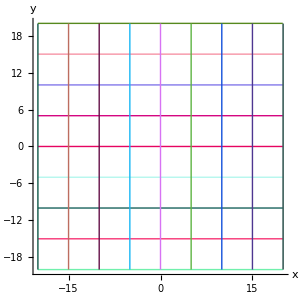
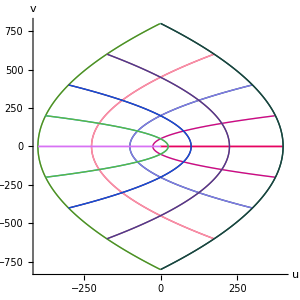

```mathematica
gridPts=makeGridPts[-20,20,.1,5];
gridColors=makeRandomColors[gridPts];
makeImage[gridPts,z^2,Automatic,10,gridColors]
```

```mathematica
gridPts[[1]][[1]]
```

{-20.,-20}

```mathematica
complexTo3D[point_]:=Module[{x,y,z,mix,X,Y,Z},
x=point[[1]];
y=point[[2]];
mix=(2x+ⅈ 2y)/(1+x^2+y^2);
X=Re[mix];
Y=Im[mix];
z=x+ⅈ y;
Z=(Abs[z]^2-1)/(Abs[z]^2+1);
Return[{X,Y,Z}]
]
```

```mathematica
complexTo3D[{1,1}]
```

{2/3,2/3,1/3}

```mathematica
pts3D=complexTo3D[#]&/@#&/@gridPts;
colors3D=makeRandomColors[pts3D]
```

{RGBColor[0.6019700656488916, 0.7852510316257038, 0.6116356248505732],RGBColor[0.06315711112614153, 0.512745189324598, 0.4131527175425078],RGBColor[0.02193270323910057, 0.5744028155877241, 0.6668721072776738],RGBColor[0.6862751082551148, 0.4981864670063254, 0.27574294863658144],RGBColor[0.5705912674883906, 0.4107555950587283, 0.951211218758655],RGBColor[0.7208174232263016, 0.80563955326471, 0.40777266149875335],RGBColor[0.38109903624066876, 0.0643690205798586, 0.66874666809981],RGBColor[0.939383478755405, 0.25944738173310666, 0.6261944295894057],RGBColor[0.3026414089412113, 0.8666232453769211, 0.8523897494056396],RGBColor[0.7462232610646087, 0.8253963486183755, 0.41997393255985416],RGBColor[0.394479022146518, 0.09941505236228187, 0.02176813461690741],RGBColor[0.6508298006526541, 0.09063220414738637, 0.33247638784413414],RGBColor[0.23857274584695043, 0.9710803347954391, 0.24456742551211508],RGBColor[0.40786756355849985, 0.9511354451662879, 0.31425571066373426],RGBColor[0.8651653513003794, 0.4309284303135017, 0.047300305434216705],RGBColor[0.6903596594918129, 0.6351803133623979, 0.6304344077291626],RGBColor[0.9816481120358027, 0.3722935612266054, 0.9690391738841768],RGBColor[0.38729207757120077, 0.9816775316045332, 0.11229215159249972]}

```mathematica
ListPointPlot3D[pts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,pts3D}]]
```

-Graphics3D-

### 1 to 100 log spaced

```mathematica
fSpace[min_,max_,steps_,f_: Log]:=Module[{},N[InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]]]
```

```mathematica
Re@fSpace[-20,20,100]
```

{-20.,-19.9899,-19.9597,-19.9094,-19.8391,-19.7488,-19.6386,-19.5086,-19.359,-19.1899,-19.0014,-18.7939,-18.5674,-18.3222,-18.0585,-17.7767,-17.477,-17.1597,-16.8251,-16.4735,-16.1054,-15.7211,-15.3209,-14.9053,-14.4747,-14.0295,-13.5702,-13.0972,-12.6111,-12.1122,-11.6011,-11.0784,-10.5445,-10.,-9.44542,-8.88133,-8.3083,-7.7269,-7.13772,-6.54136,-5.93841,-5.32948,-4.71518,-4.09613,-3.47296,-2.8463,-2.21676,-1.585,-0.951638,-0.317319,0.317319,0.951638,1.585,2.21676,2.8463,3.47296,4.09613,4.71518,5.32948,5.93841,6.54136,7.13772,7.7269,8.3083,8.88133,9.44542,10.,10.5445,11.0784,11.6011,12.1122,12.6111,13.0972,13.5702,14.0295,14.4747,14.9053,15.3209,15.7211,16.1054,16.4735,16.8251,17.1597,17.477,17.7767,18.0585,18.3222,18.5674,18.7939,19.0014,19.1899,19.359,19.5086,19.6386,19.7488,19.8391,19.9094,19.9597,19.9899,20.}

```mathematica
Range[-1,1,(1-(-1))/(20-1)]
```

{-1,-17/19,-15/19,-13/19,-11/19,-9/19,-7/19,-5/19,-3/19,-1/19,1/19,3/19,5/19,7/19,9/19,11/19,13/19,15/19,17/19,1}

## Log grid Riemann sphere

```mathematica
ptsPerLine=100;
numLines=5;
min=-10000;
max=10000;
expr=z^3
```

z^3

```mathematica
logGridPts=makeLogGridPts[min,max,ptsPerLine,numLines];
Dimensions[logGridPts]
```

{10,100,2}

```mathematica
logPts3D=pts3D=complexTo3D[#]&/@#&/@logGridPts;
Dimensions[logPts3D]
```

{10,100,3}

```mathematica
colors3D=makeRandomColors[logPts3D]
```

{RGBColor[0.8001414668325082, 0.08138458130914494, 0.05408402912071386],RGBColor[0.589463045039371, 0.8127321642383074, 0.20963026641692917],RGBColor[0.7297483079600449, 0.41051622270032495, 0.39432163234267326],RGBColor[0.05467274875743766, 0.5954252324264644, 0.6082182910983558],RGBColor[0.059376203911643444, 0.25084109299226354, 0.47520615901177465],RGBColor[0.865849111073312, 0.2090653559367921, 0.6755717725302275],RGBColor[0.7569911199681749, 0.9494446605213775, 0.8631597379852061],RGBColor[0.13838375193092234, 0.06832462608077638, 0.45233153796329195],RGBColor[0.6043370762726257, 0.28238058293893076, 0.7386410941758814],RGBColor[0.1906704885819115, 0.34900930026916277, 0.9398499620575071]}

```mathematica
ListPointPlot3D[logPts3D,PlotRange->All,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[MapThread[{#1,Thick,Line[#2]}&,{colors3D,pts3D}]]
```

-Graphics3D-

## Trying to get circular spaced points

```mathematica
Clear[makeRiemannUnitCirclePts]
```

```mathematica
makeRiemannUnitCirclePts[numPts_]:=Module[
{angles, pts},
angles=N@Range[0Pi,2Pi,(2 Pi - 0Pi)/(numPts - 1)];
pts=Table[{Cos[ang],0,Sin[ang]},{ang,angles}];
Return[pts]
]
```

```mathematica
riemannPointToComplexPlane[{X_,Y_,Z_}]:=Module[{sol,pair},
sol=Solve[{x+ⅈ y==(X+ⅈ Y)/(1-Z)},{x∈Reals,y∈Reals}];
pair=({x,y}/.sol)[[1]];
Return[pair]
]
```

```mathematica
makeSphereSpacedPoints[numPts_]:=Module[{pts,complexPts,realPts},
pts=makeRiemannUnitCirclePts[numPts];
complexPts=riemannPointToComplexPlane[#]&/@pts;
realPts=complexPts[[All,1]];
Return[realPts]
]
```

{1.,1.40059,2.04553,3.35894,8.02247,-24.1778,-4.76922,-2.56278,-1.67822,-1.1807,-0.846957,-0.595871,-0.390201,-0.209678,-0.0413603,0.12465,0.297713,0.48887,0.713986,1.}

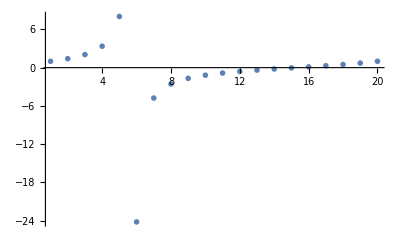

```mathematica
sphericalPts=makeSphereSpacedPoints[20]
ListPlot[sphericalPts,PlotStyle->PointSize[.01],PlotRange->All]
```

```mathematica
makeSphereSpacedPoints[20]
```

{1.,1.40059,2.04553,3.35894,8.02247,-24.1778,-4.76922,-2.56278,-1.67822,-1.1807,-0.846957,-0.595871,-0.390201,-0.209678,-0.0413603,0.12465,0.297713,0.48887,0.713986,1.}

```mathematica
horiPts=Table[Table[{x,y},{x,{1.,1.4005871438998048,2.045532694709038,3.3589407898715407,8.022471262465187,-24.177770864938736,-4.769218689284606,-2.5627803610641804,-1.67821653689189,-1.1806977689241733,-0.8469567964977006,-0.5958706627048448,-0.3902012108383555,-0.20967795044642917,-0.04136030594326412,0.12464987000685275,0.2977128989636771,0.4888702109658738,0.7139862766522278,0.9999999999999998}}],{y,-1,1,(1-(-1))/(2-1)}]
```

{{{1.,-1},{1.40059,-1},{2.04553,-1},{3.35894,-1},{8.02247,-1},{-24.1778,-1},{-4.76922,-1},{-2.56278,-1},{-1.67822,-1},{-1.1807,-1},{-0.846957,-1},{-0.595871,-1},{-0.390201,-1},{-0.209678,-1},{-0.0413603,-1},{0.12465,-1},{0.297713,-1},{0.48887,-1},{0.713986,-1},{1.,-1}},{{1.,1},{1.40059,1},{2.04553,1},{3.35894,1},{8.02247,1},{-24.1778,1},{-4.76922,1},{-2.56278,1},{-1.67822,1},{-1.1807,1},{-0.846957,1},{-0.595871,1},{-0.390201,1},{-0.209678,1},{-0.0413603,1},{0.12465,1},{0.297713,1},{0.48887,1},{0.713986,1},{1.,1}}}

```mathematica
Clear[makeHorizontalLines]
```

```mathematica
makeHorizontalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts,spherePts},
spherePts=makeSphereSpacedPoints[ptsPerLine];
horiPts=Table[Table[{x,y},{x,spherePts}],{y,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeVerticalLines[min_,max_,ptsPerLine_,numLines_]:=Module[{horiPts,spherePts},
spherePts=makeSphereSpacedPoints[ptsPerLine];
horiPts=Table[Table[{x,y},{y,spherePts}],{x,min,max,(max-min)/(numLines-1)}];
Return[horiPts]
]
makeGrid[min_,max_,ptsPerLine_,numLines_]:=Module[{vertPts,horiPts,pts},
vertPts=makeHorizontalLines[min,max,ptsPerLine,numLines];
horiPts=makeVerticalLines[min,max,ptsPerLine,numLines];
pts=Join[horiPts,vertPts];
Return[pts]
]
```

```mathematica
min=-3;
max=3;
ptsPerLine=200;
numLines=3;
```

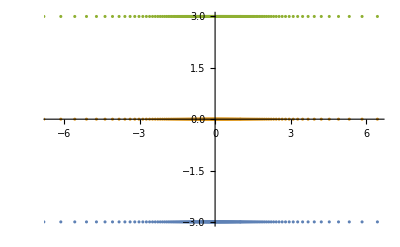

```mathematica
horiPts=makeHorizontalLines[min,max,ptsPerLine,numLines];
ListPlot[horiPts]
```

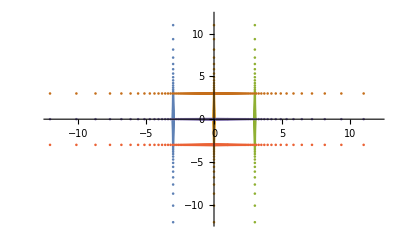

```mathematica
gridPts=makeGrid[min,max,ptsPerLine,numLines];
ListPlot[gridPts]
```

```mathematica
spherePts3D=complexTo3D[#]&/@#&/@gridPts;
colors2=makeRandomColors[spherePts3D]
```

{RGBColor[0.44894834872124867, 0.03553841222977838, 0.5596750368193348],RGBColor[0.7787357837897411, 0.5834420250087362, 0.5106463523034201],RGBColor[0.6504361112264501, 0.4917050455987646, 0.41115859407933586],RGBColor[0.920618705480007, 0.35242110642718316, 0.023244663455393555],RGBColor[0.7174276249470612, 0.4332720441180964, 0.8727773285640565],RGBColor[0.9477850646033359, 0.8022929418768905, 0.33710733636441104]}

```mathematica
ListPointPlot3D[spherePts3D,PlotRange->Full,AspectRatio->1,ImageSize->Large]
```

-Graphics3D-

-Graphics3D-

```mathematica
Dimensions[spherePts3D]
```

{6,200,3}

200

```mathematica
takingPts[takes_,pts_]:=Module[{newPts},
newPts=Take[pts,#]&/@takes;
Return[newPts]]
```

```mathematica
cylinderPts[pts_]:=Module[{takes,returnPts},
takes=Table[{x,x+1},{x,1,Dimensions[pts][[2]]-1}];
returnPts=takingPts[takes,#]&/@spherePts3D
]
cylinders[pts_]:=Module[{},
Return[Cylinder[#,.02]&/@#&/@cylinderPts[pts]]]
```

```mathematica
Export["grid.stl",Graphics3D[cylinders[spherePts3D],{"STL,","BinaryFormat"->True}]]
```

grid.stl

```mathematica
Import["grid.stl"]
```

-Graphics3D-